```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
"C:\\Users\\Jieyu You\\Google Drive\\multi atom\\origin spec"
```

C:\Users\Jieyu You\Google Drive\multi atom\origin spec

```mathematica
Plot[Λ [Abs[t]],{t,0.05,0.1}]
```

```mathematica
ρ[t_]:=Table[a[i,j][t],{i,4},{j,4}]
cij[t_]:=Table[c[i,j][t],{i,4},{j,4}]
slnn=Flatten[Table[a[i,j][t],{i,4},{j,4}]];
slnc=Flatten[Table[c[i,j][t],{i,4},{j,4}]];
(*basis:a1a2,a1b2,b1a2,b1b2*)
(*λ0=1;
k0=2Pi/λ0;
b=1.2 λ0/2(*max*);
k0z=√(((2Pi)/λ0)^2-(Pi/b)^2);*)
k0z=1;
λ0z=2Pi/k0z;
n=0.;
 θ=Pi/2-1*k0z n λ0z;rr=0.5;
r1=(-0.0+0)λ0z;r2=(0.05+0)λ0z;
kz0rc=0Pi/8;
damp=0.;
ΩR1=4;ΩR2=4;
inity=({{1, -I, -I, -1}, {I, 1, 1, -I}, {I, 1, 1, -I}, {-1, I, I, 1}})/4(*(e1-ig1)(e2-ig2)*);
initx=1/4ConstantArray[1,{4,4}];(*(e1+g1)(e2+g2)*)
initxx=({{1, -1, -1, 1}, {-1, 1, 1, -1}, {-1, 1, 1, -1}, {1, -1, -1, 1}})/4(*(e1-g1)(e2-g2)*);
init=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})(*e1g2*);
initdp=({{1, (1-ⅈ)/(√2), (1-ⅈ)/(√2), -ⅈ}, {(1+ⅈ)/(√2), 1, 1, (1-ⅈ)/(√2)}, {(1+ⅈ)/(√2), 1, 1, (1-ⅈ)/(√2)}, {ⅈ, (1+ⅈ)/(√2), (1+ⅈ)/(√2), 1}})/4(*(1/√2e+(1/2+1/2i)g)*);
init1=({{0, 0, 0, 0}, {0, 1, 0, 1}, {0, 0, 0, 0}, {0, 1, 0, 1}})/2;initi=({{0, 0, 0, 0}, {0, 1, 0, I}, {0, 0, 0, 0}, {0, -I, 0, 1}})/2;(*(e1-ig1)g2*)
init1e=({{1, 0, 1, 0}, {0, 0, 0, 0}, {1, 0, 1, 0}, {0, 0, 0, 0}})/2;initie=({{1, 0, I, 0}, {0, 0, 0, 0}, {-I, 0, 1, 0}, {0, 0, 0, 0}})/2;(*(e1-ig1)e2*)
initetg=({{1, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 1}})/2;(*e1e2+g1g2*)
initee=({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
initgg=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}});
initetg2=({{0, 0, 0, 0}, {0, 1, -1, 0}, {0, -1, 1, 0}, {0, 0, 0, 0}})/2;(*e1g2+g1e2*)




x=r2-r1;(*r1 r2 along z dirction *)

(*second variable:1=p, 0=m*)
σ[1,1]=({{0, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});(*|e1><g1|*)σ[1,0]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}});(*|g1><e1|*)
σ[2,1]=({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}});(*|e2><g2|*)σ[2,0]=({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}});(*|g2><e2|*)

Do[bra={{0},{0},{0},{0}};ket={{0,0,0,0}};bra[[i,1]]=1;ket[[1,j]]=1;xij[i,j]=bra.ket,{i,1,4},{j,1,4}]


V=(ΩR1 Exp[-I θ]Exp[-I k0z r1]σ[1,0]+ΩR1 Exp[I θ]Exp[I k0z r1]σ[1,1]+Exp[-I θ]ΩR2 Exp[-I k0z r2]σ[2,0]+Exp[I θ]ΩR2 Exp[I k0z r2]σ[2,1])/2;(*running wave*)
(*V=(ΩR1 Exp[-I θ]σ[1,0]+ΩR1 Exp[I θ]σ[1,1]+Exp[-I θ]ΩR2 σ[2,0]+Exp[I θ]ΩR2 σ[2,1])/2;(*standing wave*)*)

sh=Sinh[rr];
ch=Cosh[rr];
ϕ=0;

(*F[r_]:=F[r]=3/2(Sin[k0 r]/(k0 r)+(Cos[k0 r]/(k0 r)^2-Sin[k0 r]/(k0 r)^3));
Λ[r_]:=Λ[r]=3/4(-Cos[k0 r]/(k0 r)+(Sin[k0 r]/(k0 r)^2+Cos[k0 r]/(k0 r)^3));
γ[1,1]=γ[2,2]=1;
γs[1,1]=γs[2,2]=1;
γ[1,2]=F[r2-r1];γ[2,1]=F[r2-r1];
γs[1,2]=F[r2-r1];γs[2,1]=F[r2-r1];
γp[1,1]=F[r1+r1] ;γp[2,2]=F[r2+r2];
γps[1,1]=F[r1+r1] ;γps[2,2]=F[r2+r2];
γp[1,2]=F[r1+r2];γp[2,1]=F[r1+r2];
γps[1,2]=F[r1+r2];γps[2,1]=F[r1+r2];(*4 sln to 4 init*)*)

(*γ[1,1]=γ[2,2]=1;
γs[1,1]=γs[2,2]=1;
γ[1,2]=0;γ[2,1]=2Exp[I k0z(r2-r1)];
γs[1,2]=0;γs[2,1]=2Exp[-I k0z(r2-r1)];
γp[1,1]=Exp[2I k0z r1] ;γp[2,2]=Exp[2I k0z r2];
γps[1,1]=Exp[-2I k0z r1] ;γps[2,2]=Exp[-2I k0z r2];
γp[1,2]=0;γp[2,1]=2Exp[I k0z(r1+r2)];
γps[1,2]=0;γps[2,1]=2Exp[-I k0z(r1+r2)];
Λ[r_]:=Λ[r]=0;*)(*unidirectional waveguide*)

γ[1,1]=γ[2,2]=1;
γs[1,1]=γs[2,2]=1;
γ[1,2]=Exp[I k0z(r2-r1)];γ[2,1]=Exp[I k0z(r2-r1)];
γs[1,2]=Exp[-I k0z(r2-r1)];γs[2,1]=Exp[-I k0z(r2-r1)];
γp[1,1]=Cos[2 k0z r1] ;γp[2,2]=Cos[2 k0z r2];
γps[1,1]=Cos[-2k0z r1] ;γps[2,2]=Cos[-2 k0z r2];
γp[1,2]=Exp[-I k0z(r1+r2)];γp[2,1]=Exp[I k0z(r1+r2)];
γps[1,2]=Exp[I k0z(r1+r2)];γps[2,1]=Exp[-I k0z(r1+r2)];Λ[r_]:=Λ[r]=0;(*normal waveguide*)
SQ=-0.5sh ch(Sum[γp[i,j](Exp[2I kz0rc]ρ[t].σ[i,1].σ[j,1]+Exp[2I kz0rc]σ[i,1].σ[j,1].ρ[t]-Exp[2I kz0rc]σ[i,1].ρ[t].σ[j,1]-Exp[2I kz0rc]σ[j,1].ρ[t].σ[i,1])+γps[i,j](Exp[-2I kz0rc]ρ[t].σ[j,0].σ[i,0]+Exp[-2I kz0rc]σ[j,0].σ[i,0].ρ[t]-Exp[-2I kz0rc]σ[j,0].ρ[t].σ[i,0]-Exp[-2I kz0rc]σ[i,0].ρ[t].σ[j,0]),{i,1,2},{j,1,2}])-0.5(sh^2+1)Sum[γ[i,j](σ[i,1].σ[j,0].ρ[t]-σ[j,0].ρ[t].σ[i,1])+γs[i,j](ρ[t].σ[j,1].σ[i,0]-σ[i,0].ρ[t].σ[j,1]),{i,1,2},{j,1,2}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[j,0].σ[i,1]-σ[i,1].ρ[t].σ[j,0])+γs[i,j](σ[i,0].σ[j,1].ρ[t]-σ[j,1].ρ[t].σ[i,0]),{i,1,2},{j,1,2}]-I Λ [Abs[r1-r2]](σ[1,1].σ[2,0].ρ[t]+σ[2,1].σ[1,0].ρ[t]-ρ[t].σ[1,1].σ[2,0]-ρ[t].σ[2,1].σ[1,0])-0.5 damp(sh^2+1)Sum[γ[i,i](σ[i,1].σ[i,0].ρ[t]-σ[i,0].ρ[t].σ[i,1])+γs[i,i](ρ[t].σ[i,1].σ[i,0]-σ[i,0].ρ[t].σ[i,1]),{i,1,2}]-0.5 damp sh^2Sum[γ[i,i](ρ[t].σ[i,0].σ[i,1]-σ[i,1].ρ[t].σ[i,0])+γs[i,i](σ[i,0].σ[i,1].ρ[t]-σ[i,1].ρ[t].σ[i,0]),{i,1,2}];
SQc=-0.5sh ch(Sum[γp[i,j](cij[t].σ[i,1].σ[j,1]+σ[i,1].σ[j,1].cij[t]-σ[i,1].cij[t].σ[j,1]-σ[j,1].cij[t].σ[i,1])+γps[i,j](cij[t].σ[j,0].σ[i,0]+σ[j,0].σ[i,0].cij[t]-σ[j,0].cij[t].σ[i,0]-σ[i,0].cij[t].σ[j,0]),{i,1,2},{j,1,2}])-0.5(sh^2+1)Sum[γ[i,j](σ[i,1].σ[j,0].cij[t]-σ[j,0].cij[t].σ[i,1])+γs[i,j](cij[t].σ[j,1].σ[i,0]-σ[i,0].cij[t].σ[j,1]),{i,1,2},{j,1,2}]-0.5 sh^2Sum[γ[i,j](cij[t].σ[j,0].σ[i,1]-σ[i,1].cij[t].σ[j,0])+γs[i,j](σ[i,0].σ[j,1].cij[t]-σ[j,1].cij[t].σ[i,0]),{i,1,2},{j,1,2}] -I Λ [Abs[r1-r2]](σ[1,1].σ[2,0].cij[t]+σ[2,1].σ[1,0].cij[t]-cij[t].σ[1,1].σ[2,0]-cij[t].σ[2,1].σ[1,0])-0.5 damp(sh^2+1)Sum[γ[i,i](σ[i,1].σ[i,0].cij[t]-σ[i,0].cij[t].σ[i,1])+γs[i,i](cij[t].σ[i,1].σ[i,0]-σ[i,0].cij[t].σ[i,1]),{i,1,2}]-0.5 damp sh^2Sum[γ[i,i](cij[t].σ[i,0].σ[i,1]-σ[i,1].cij[t].σ[i,0])+γs[i,i](σ[i,0].σ[i,1].cij[t]-σ[i,1].cij[t].σ[i,0]),{i,1,2}];

DR=-I (V.ρ[t]-ρ[t].V);
DRc=-I (V.cij[t]-cij[t].V);

solsq=NDSolve[{ρ'[t]==SQ+DR,ρ[0]==init},slnn,{t,0,1000}];
initc=(σ[1,0]+σ[2,0]).(ρ[t]/.solsq/.t->500)[[1]];
solc=NDSolve[{cij'[t]==SQc+DRc,cij[0]==initc},slnc,{t,0,1000}];
(*solc=NDSolve[{Transpose[cij'[t]]==SQc+DRc,cij[0]==initc},slnc,{t,0,1000}];*)



SQs=-0.5sh ch(Sum[γp[i,i](ρ[t].σ[i,1].σ[i,1]+σ[i,1].σ[i,1].ρ[t]-σ[i,1].ρ[t].σ[i,1]-σ[i,1].ρ[t].σ[i,1])+γps[i,i](ρ[t].σ[i,0].σ[i,0]+σ[i,0].σ[i,0].ρ[t]-σ[i,0].ρ[t].σ[i,0]-σ[i,0].ρ[t].σ[i,0]),{i,1,2}])-0.5(sh^2+1)Sum[γ[i,i](σ[i,1].σ[i,0].ρ[t]-σ[i,0].ρ[t].σ[i,1])+γs[i,i](ρ[t].σ[i,1].σ[i,0]-σ[i,0].ρ[t].σ[i,1]),{i,1,2}]-0.5 sh^2Sum[γ[i,i](ρ[t].σ[i,0].σ[i,1]-σ[i,1].ρ[t].σ[i,0])+γs[i,i](σ[i,0].σ[i,1].ρ[t]-σ[i,1].ρ[t].σ[i,0]),{i,1,2}] ;
SQsc=-0.5sh ch(Sum[γp[i,i](cij[t].σ[i,1].σ[i,1]+σ[i,1].σ[i,1].cij[t]-σ[i,1].cij[t].σ[i,1]-σ[i,1].cij[t].σ[i,1])+γps[i,i](cij[t].σ[i,0].σ[i,0]+σ[i,0].σ[i,0].cij[t]-σ[i,0].cij[t].σ[i,0]-σ[i,0].cij[t].σ[i,0]),{i,1,2}])-0.5(sh^2+1)Sum[γ[i,i](σ[i,1].σ[i,0].cij[t]-σ[i,0].cij[t].σ[i,1])+γs[i,i](cij[t].σ[i,1].σ[i,0]-σ[i,0].cij[t].σ[i,1]),{i,1,2}]-0.5 sh^2Sum[γ[i,i](cij[t].σ[i,0].σ[i,1]-σ[i,1].cij[t].σ[i,0])+γs[i,i](σ[i,0].σ[i,1].cij[t]-σ[i,1].cij[t].σ[i,0]),{i,1,2}] ;

solsqs=NDSolve[{ρ'[t]==SQs+DR,ρ[0]==init},slnn,{t,0,1000}];
initsc=(σ[1,0]+σ[2,0]).(ρ[t]/.solsqs/.t->500)[[1]];
solsc=NDSolve[{cij'[t]==SQsc+DRc,cij[0]==initsc},slnc,{t,0,1000}];

TH=-0.5(sh^2+1)Sum[γ[i,j](σ[i,1].σ[j,0].ρ[t]-σ[j,0].ρ[t].σ[i,1])+γs[i,j](ρ[t].σ[j,1].σ[i,0]-σ[i,0].ρ[t].σ[j,1]),{i,1,2},{j,1,2}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[j,0].σ[i,1]-σ[i,1].ρ[t].σ[j,0])+γs[i,j](σ[i,0].σ[j,1].ρ[t]-σ[j,1].ρ[t].σ[i,0]),{i,1,2},{j,1,2}]-I Λ [Abs[r1-r2]](σ[1,1].σ[2,0].ρ[t]+σ[2,1].σ[1,0].ρ[t]-ρ[t].σ[1,1].σ[2,0]-ρ[t].σ[2,1].σ[1,0])-0.5 damp(sh^2+1)Sum[γ[i,i](σ[i,1].σ[i,0].ρ[t]-σ[i,0].ρ[t].σ[i,1])+γs[i,i](ρ[t].σ[i,1].σ[i,0]-σ[i,0].ρ[t].σ[i,1]),{i,1,2}]-0.5 damp sh^2Sum[γ[i,i](ρ[t].σ[i,0].σ[i,1]-σ[i,1].ρ[t].σ[i,0])+γs[i,i](σ[i,0].σ[i,1].ρ[t]-σ[i,1].ρ[t].σ[i,0]),{i,1,2}];
THc=-0.5(sh^2+1)Sum[γ[i,j](σ[i,1].σ[j,0].cij[t]-σ[j,0].cij[t].σ[i,1])+γs[i,j](cij[t].σ[j,1].σ[i,0]-σ[i,0].cij[t].σ[j,1]),{i,1,2},{j,1,2}]-0.5 sh^2Sum[γ[i,j](cij[t].σ[j,0].σ[i,1]-σ[i,1].cij[t].σ[j,0])+γs[i,j](σ[i,0].σ[j,1].cij[t]-σ[j,1].cij[t].σ[i,0]),{i,1,2},{j,1,2}] -I Λ [Abs[r1-r2]](σ[1,1].σ[2,0].cij[t]+σ[2,1].σ[1,0].cij[t]-cij[t].σ[1,1].σ[2,0]-cij[t].σ[2,1].σ[1,0])-0.5 damp(sh^2+1)Sum[γ[i,i](σ[i,1].σ[i,0].cij[t]-σ[i,0].cij[t].σ[i,1])+γs[i,i](cij[t].σ[i,1].σ[i,0]-σ[i,0].cij[t].σ[i,1]),{i,1,2}]-0.5 damp sh^2Sum[γ[i,i](cij[t].σ[i,0].σ[i,1]-σ[i,1].cij[t].σ[i,0])+γs[i,i](σ[i,0].σ[i,1].cij[t]-σ[i,1].cij[t].σ[i,0]),{i,1,2}];

solTH=NDSolve[{ρ'[t]==TH+DR,ρ[0]==init},slnn,{t,0,1000}];
initTHc=(σ[1,0]+σ[2,0]).(ρ[t]/.solTH/.t->500)[[1]];
solTHc=NDSolve[{cij'[t]==THc+DRc,cij[0]==initTHc},slnc,{t,0,1000}];
```

```mathematica
"
```

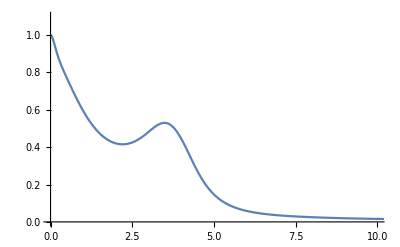

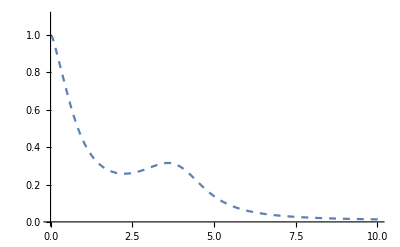

```mathematica
ss=Tr[((cij[t]/.solc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]/.t->500;
sss=Tr[((cij[t]/.solTHc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]/.t->500;
spectrum=Re[InverseFourier[Table[Tr[((cij[t]/.solc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]-ss,{t,0,150Pi,0.01}]]];
spectrums=Re[InverseFourier[Table[Tr[((cij[t]/.solTHc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]-sss,{t,0,100Pi,0.01}]]];
vac=ListLinePlot[spectrum/spectrum[[1]],DataRange->{0,2Pi 100},PlotRange->{{0,10},{0,1.1}},PlotLegends->"vac"]
vacs=ListLinePlot[spectrums/spectrums[[1]],DataRange->{0,2Pi 100},PlotRange->{{0,10},{0,1.1}},PlotStyle->{Dashed},PlotLegends->"vac"]
```

```mathematica
ss=Tr[((cij[t]/.solc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]/.t->1000;
sss=Tr[((cij[t]/.solTHc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]/.t->1000;
spectrum=Re[Fourier[Table[Tr[((cij[t]/.solc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]-ss,{t,0,100Pi,0.01}]]];
spectrums=Re[Fourier[Table[Tr[((cij[t]/.solTHc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]-sss,{t,0,100Pi,0.01}]]];
sq0=ListLinePlot[spectrum/spectrum[[1]],DataRange->{0,2Pi 100},PlotRange->{{0,100},{0,1.1}},PlotStyle->{Red},PlotLegends->"0"]
sq0s=ListLinePlot[spectrums/spectrums[[1]],DataRange->{0,2Pi 100},PlotRange->{{0,100},{0,1.1}},PlotStyle->{Red,Dashed},PlotLegends->"0"]
```

```mathematica
ss=Tr[((cij[t]/.solc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]/.t->1000;
sss=Tr[((cij[t]/.solTHc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]/.t->1000;
spectrum=Re[Fourier[Table[Tr[((cij[t]/.solc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]-ss,{t,0,100Pi,0.01}]]];
spectrums=Re[Fourier[Table[Tr[((cij[t]/.solTHc)[[1]].(xij[1,2]+xij[1,3]+xij[2,4]+xij[3,4]))]-sss,{t,0,100Pi,0.01}]]];
sq1=ListLinePlot[spectrum/spectrum[[1]],DataRange->{0,2Pi 100},PlotRange->{{0,100},{0,1.1}},PlotStyle->{Green},PlotLegends->"Pi/2"]
sq1s=ListLinePlot[spectrums/spectrums[[1]],DataRange->{0,2Pi 100},PlotRange->{{0,100},{0,1.1}},PlotStyle->{Green,Dashed},PlotLegends->"Pi/2"]
```

```mathematica
Show[{vac,sq0,sq1,vacs,sq0s,sq1s}]
```

```mathematica
Plot[{{{0, 0, 0, 1}}.(ρ[t]/.solsq)[[1]].{{0}, {0}, {0}, {1}},{{1, 0, 0, 0}}.(ρ[t]/.solsq)[[1]].{{1}, {0}, {0}, {0}},{{0, 1, 1, 0}}.(ρ[t]/.solsq)[[1]].{{0}, {1}, {1}, {0}}/2,{{0, 1, -1, 0}}.(ρ[t]/.solsq)[[1]].{{0}, {1}, {-1}, {0}}/2},{t,0,8},PlotRange->{0,0.8},PlotLegends->{"gg","ee","eg+ge","eg-ge"}]
```

```mathematica
Plot[{{{1, 0, 0, 1}}.(ρ[t]/.solsq)[[1]].{{1}, {0}, {0}, {1}}/2,{{1, 0, 0, -1}}.(ρ[t]/.solsq)[[1]].{{1}, {0}, {0}, {-1}}/2,{{0, 1, 1, 0}}.(ρ[t]/.solsq)[[1]].{{0}, {1}, {1}, {0}}/2,{{0, 1, -1, 0}}.(ρ[t]/.solsq)[[1]].{{0}, {1}, {-1}, {0}}/2},{t,0,10},PlotRange->{0,0.8},PlotLegends->{"ee+gg","ee-gg","eg+ge","eg-ge"}]
```